# Exploring group theory with mathematica : from music to particles

## Jules Charlier, Rafael Salavarria Lorenzoni, Oscar Eatwell, Jawad Ben Brahim

## group theory : basics

Very simple and powerful idea :

A set of elements and a binary operation  :    et

Closure : no matter how you group the steps, the outcome is always an element of

Associativity :

A neutral element :

Every element has an inverse :

group 

Some groups are “Abelian” :

Commutativity :

A whole universe :

Finite of infinite, simple of incredibly complex

## Cayley table

Makes the structure visible, like a multiplication table

```mathematica
ColouredCayleyTable[{"AddMod", 6}]
```

Addition Mod 6 | 0 | 1 | 2 | 3 | 4 | 5
0 | 0 | 1 | 2 | 3 | 4 | 5
1 | 1 | 2 | 3 | 4 | 5 | 0
2 | 2 | 3 | 4 | 5 | 0 | 1
3 | 3 | 4 | 5 | 0 | 1 | 2
4 | 4 | 5 | 0 | 1 | 2 | 3
5 | 5 | 0 | 1 | 2 | 3 | 4

```mathematica
Quiet@CayleyMultiplicationTable[AbelianGroup[{2,4}]]
Quiet@CayleyMultiplicationTable[CyclicGroup[5]]
Quiet@CayleyMultiplicationTable[{"AddMod",7}]
Quiet@CayleyMultiplicationTable[{"MultMod",8}]
Quiet@CayleyMultiplicationTable[DihedralGroup[3]]
Quiet@CayleyMultiplicationTable[{"And","BooleanDomain"}]
```

## Generators

### Musical scales and intervals, and generators

Traditionnaly in music theory an octave is deivided into 12 named intervals. After which we loop back to the unison, which means it behaves similarly to ℤ/12ℤ
Un octave en théorie de la musique est divisé en 12 intervalles égaux. Après la 7e majeure, on revient à l’unison, ainsi l’ensemble des intervalles se comporte similairement à ℤ/12ℤ

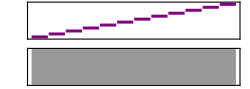

```mathematica
Sound[Table[SoundNote[n,0.5],{n,0,11}]]
```

If we consider the operation of stacking two intervals on top of each other as a group operation, then this scale is isomorphic to (ℤ/12ℤ,+)≅C_12, which we can represent in a Cailey table:
Si l’on considère l’opération de superposer deux intervalles comme l’opération du groupe, alors l’ensemble est isomorphique à (ℤ/12ℤ,+)≅C_12, que l’on peut représenter dans la table de Cailey:

```mathematica
TableForm[GroupMultiplicationTable[CyclicGroup[12]] -1,TableHeadings->{Range[0,11],Range[0,11]}]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
0 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0
2 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1
3 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2
4 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3
5 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4
6 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5
7 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6
8 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
9 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
10 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
11 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

Let’s try to stack the same interval on top of itself many times, and see the intervals we get by this process:
Essayons de superposer un intervalle sur lui-même un certain nombre de fois et observons le résultat:

```mathematica
Manipulate[
Column[
{
Sound[
{Table[SoundNote[Mod[k n,12],1],{k,0,11}]}
],
UniqueElements[{Table[Mod[k n,12],{k,0,11}]}][[1]]
}
],
{n,0,11,1}
]
```

```mathematica
Manipulate[
Column[
{
StringJoin["PGCD(",ToString[n],",12) = ",ToString[GCD[12,n]]],
UniqueElements[{Table[Mod[k n,12],{k,12}]}][[1]]
}
],
{n,0,11,1}
]
```

```mathematica
Manipulate[
Column[
{
StringJoin["12 / PGCD(",ToString[n],",12) = ",ToString[12/GCD[12,n]]],
UniqueElements[{Table[Mod[k n,12],{k,12}]}][[1]]
}
],
{n,0,11,1}
]
```

```mathematica
{b,c}=N@{E^((-Log[220]+Log[440])/12),(3 (-3 Log[220]-Log[440]))/(Log[220]-Log[440])};
frequency[x_?NumericQ]:=b^(x+c)
Manipulate[
Column[{
Module[
{tones},
tones=Table[
With[
{k=n},
Play[
Sin[2 Pi t*frequency[12.0*Mod[l k,m]/m]],
{t,0,0.5},
SampleRate->8000
]
],
{n,0,m-1}
];
Sound[tones]
],
ToString[m]<>" / GCD("<>ToString[l]<>", "<>ToString[m]<>") = "<>ToString[m/GCD[m,l]],
UniqueElements[{Table[Mod[k l,m],{k,0,m-1}]}][[1]],
"ϕ["<>ToString[m]<>"] = "<>ToString[EulerPhi[m]]
}],
{{m,12},2,30,1},
{{l,1},0,m,1}
]
```

## Dihedral Groups

The textbook example of group theory are the symmertries of a regular polygon.
L’exemple traditionnel d’un groupe sont les symmétries des polygones réguliers

transfos={InfiniteLine[{{0,0},{1/2,(√3)/6}}],
InfiniteLine[{{1,0},{1/2,(√3)/6}}],
InfiniteLine[{{1/2,1},{1/2,0}}],
Arrow[Circle[{1/2,(√3)/6},0.2,{π/2,(7π)/6}]],
Arrow[Circle[{1/2,(√3)/6},0.15,{π/2,(11π)/6}]]};
triangle=
{{
Opacity[0.5],
Polygon[{
{0,0},
{1,0},
{1/2,(√3)/2}
}]},
{PointSize[Large],StandardRed,Point[{0,0}]},
{PointSize[Large],StandardGreen,Point[{1,0}]},
{PointSize[Large],StandardBlue,Point[{1/2,(√3)/2}]}
};

For the equilateral triangle:

```mathematica
Graphics[{
transfos,triangle
}]
```

-Graphics-

```mathematica
Graphics[{
transfos,
Dynamic[GeometricTransformation[
triangle,
ScalingTransform[Clock[{-1,1},5,1],{1,0},{1/2,(√3)/6}]
]
]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}}]
```

-Graphics-

s1[t_]:=ScalingTransform[2t-1,{-√3,3},{1/2,(√3)/6}]
s2[t_]:=ScalingTransform[2t-1,{√3,3},{1/2,(√3)/6}]
s3[t_]:=ScalingTransform[2t-1,{1,0},{1/2,(√3)/6}]
r1[t_]:=RotationTransform[(2π t)/3,{1/2,(√3)/6}]
r2[t_]:=RotationTransform[(4t π)/3,{1/2,(√3)/6}]

```mathematica
Graphics[{
transfos,
Dynamic[GeometricTransformation[triangle,r2[Clock[{0,1},5,1]]]
]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}}]
```

-Graphics-

The group operation will be composing two transformations. We then obtain a new transformation.

```mathematica
AnimateTransformations[transList_List,stepDur_:5]:=Module[{n=Length[transList],duration},duration=stepDur*n;
Animate[
Graphics[
{
transfos,
Fold[
(GeometricTransformation[#1,#2]&),
triangle,
Table[transList[[i]][Min[1,Max[0,(t-(i-1)*stepDur)/stepDur]]],
{i,n}
]
]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}}],
{t,0,duration},
AnimationRepetitions->1
]
];

AnimateTransformations[{s3,s2,r1},5]
```

We can also visualise the symmetries of the square:

transfos2={InfiniteLine[{{0,0},{1,1}}],
InfiniteLine[{{1,0},{0,1}}],
InfiniteLine[{{1/2,0},{1/2,1}}],
InfiniteLine[{{0,1/2},{1,1/2}}],
Arrow[Circle[{1/2,1/2},0.1,{(3π)/4,(5π)/4}]],
Arrow[Circle[{1/2,1/2},0.15,{(3π)/4,(7π)/4}]],
Arrow[Circle[{1/2,1/2},0.2,{(3π)/4,(9π)/4}]]
};
square=
{{
Opacity[0.5],
Polygon[{
{0,0},
{1,0},
{1,1},
{0,1}
}]},
{PointSize[Large],StandardRed,Point[{0,0}]},
{PointSize[Large],StandardGreen,Point[{1,0}]},
{PointSize[Large],StandardBlue,Point[{1,1}]},
{PointSize[Large],StandardYellow,Point[{0,1}]}
};

```mathematica
Graphics[{
transfos2,square
}]
```

-Graphics-

ss1[t_]:=ScalingTransform[2t-1,{1,0},{1/2,1/2}]
ss2[t_]:=ScalingTransform[2t-1,{1,1},{1/2,1/2}]
ss3[t_]:=ScalingTransform[2t-1,{0,1},{1/2,1/2}]
ss4[t_]:=ScalingTransform[2t-1,{-1,1},{1/2,1/2}]
sr1[t_]:=RotationTransform[(π t)/2,{1/2,1/2}]
sr2[t_]:=RotationTransform[π t,{1/2,1/2}]
sr3[t_]:=RotationTransform[(3π t)/2,{1/2,1/2}]

```mathematica
AnimateTransformationsSquare[transList_List,stepDur_:5]:=Module[{n=Length[transList],duration},duration=stepDur*n;
Animate[
Graphics[
{
transfos2,
Fold[
(GeometricTransformation[#1,#2]&),
square,
Table[transList[[i]][Min[1,Max[0,(t-(i-1)*stepDur)/stepDur]]],
{i,n}
]
]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}}],
{t,0,duration},
AnimationRepetitions->1
]
];

AnimateTransformationsSquare[{sr3,ss2,ss4,sr3},7]
```

## permutation groups

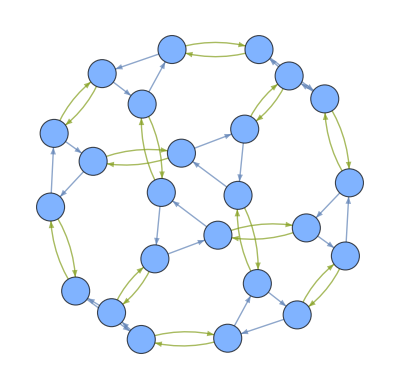

```mathematica
group = PermutationGroup[{Cycles[{{1,4,5}}],Cycles[{{3,4}}]}];
CayleyGraph[group,VertexLabels->Placed["Name",Center],VertexSize->0.7]
```

Rubik’s Cube, 15 Puzzle, etc..

## 15 Puzzle - Taquin

Example of how group theory can be found in our everyday life.

Each move - permutations of elements inside the group.

Group theory allows us to solve quickly and easily what may seem like a really hard problem.

```mathematica
fifteenPuzzle
```

Solved 15 Puzzle :

## physics

Although it is hard to see, groups also play a central role in physics.

We may as well cut out group theory. 
That is a subject that will never be of any use in physics.

Sir James Jeans

Entire structure of the Standard Model of particle physics is built from symmetry groups :
	- charges of particles
	- the way forces unify
	- possibilities of interactions

## introduction to representations

A representation ρ of a group G is a homomorphism such that:
         

GL(V)= General Linear Vector Space of dimension n - invertible linear transformations

Homomorphism is a function ρ such that:

eg:            
Group Elements = matrices - act on vectors

## group properties of invertible matrices

Identity Matrix - (1 | 0
0 | 1)
Inverse - 
Associativity- 

Note: Matrices are not necessarily commutative
These properties are only satisfied when mapping to ℂ with multiplicative (x) operation

## Representations of Zn

homomorphism mapping from ℕ+ to ℂ x (1D GL(V))

## visual representation of ZN

```mathematica
Manipulate[Graphics[Table[Point[{Re[Exp[2 Pi I n/k]],Im[Exp[2 Pi I n/k]]}],{n,0,k-1}],PlotRange->1.2,Axes->True],{k,1,100,1}]
```

## Representations of dihedral groups

```mathematica
Manipulate[Module[{v1={Cos[α],Sin[α]},v2={Cos[α+β],Sin[α+β]},θ=β,R={{Cos[β],-Sin[β]},{Sin[β],Cos[β]}},v1num,v2num},v1num=v1/. {α->αn,β->βn};
v2num=v2/. {α->αn,β->βn};
Column[{Row[{"v1 = ",TraditionalForm[v1]}],Row[{"v2 = ",TraditionalForm[v2]}],Row[{"v2 (expanded) = ",TraditionalForm[{Cos[α] Cos[β]-Sin[α] Sin[β],Sin[α] Cos[β]+Sin[β] Cos[α]}]}],Row[{"R = ",TraditionalForm@MatrixForm[R]}],Graphics[{LightGray,Circle[{0,0},1],Thick,Red,Arrow[{{0,0},v1num}],Text[Style[Row[{TraditionalForm[{Cos[α],Sin[α]}]," ≈ ",NumberForm[v1num,{4,2}]}],Red,12,Bold],v1num,{1.2,-0.6}],Thick,Blue,Arrow[{{0,0},v2num}],Text[Style[Row[{TraditionalForm[{Cos[α+β],Sin[α+β]}]," ≈ ",NumberForm[v2num,{4,2}]}],Blue,12,Bold],v2num,{-1.2,-0.6}],Black,PointSize[Medium],Point[{0,0}]},PlotRange->1.5,Axes->True,AspectRatio->1,ImageSize->380]}]],{{αn,Pi/6,"α (Initial Angle)"},0,2 Pi,Appearance->"Labeled"},{{βn,Pi/3,"β (Rotation Angle)"},0,2 Pi,Appearance->"Labeled"},TrackedSymbols:>{αn,βn}]
```

Mapping into 2D plane

## representation theory in physics

-Graphics--Graphics-

## U(1) - Internal phase rotation - electromagnetism

- similar to Zn representation

```mathematica
Manipulate[Graphics[Table[Point[{Re[Exp[2 Pi I n/k]],Im[Exp[2 Pi I n/k]]}],{n,0,k-1}],PlotRange->1.2,Axes->True],{k,1,1000,1}]
```

It’s a lie group- differentiable and continuous (sequence vs function)
Noether’s Theorem- continuous symmetry = conserved quantity - electric charge!

## particle smashing time

```mathematica
(* =====================Electroweak backbone (SU(2)_L x U(1)_Y)=====================*)(*0) Input representations for leptons:(T3,Y).*)reps=<|"eL"-><|"T3"->-1/2,"Y"->-1/2|>,"eR"-><|"T3"->0,"Y"->-1|>,"muL"-><|"T3"->-1/2,"Y"->-1/2|>,"muR"-><|"T3"->0,"Y"->-1|>|>; (* defining electromagnetic (Y) and nuclear weak (T3) interaction strengths of right and left handed muons and electrons based on representation theory*)

(*1) Charges and couplings derived from reps- use of known formulas to derive electron charge and coupling of fermions to the Z boson -axial and vector couplings (vector implements an EM correction)*)
Charge[T3_,Y_]:=T3+Y;                             (*Q=T3+Y*) 
gV[T3_,Y_,s2w_]:=T3-2 Charge[T3,Y] s2w;         (*g_V=T3-2 Q sW^2*)
gA[T3_]:=T3;                                         (*g_A=T3*) (*gA makes the Z boson coupling "chiral": different from left vs right handed fermions - property of weak interaction*)

(*2) Mixing and gauge couplings from sin^2 θ_W and α*)
MixingAndCouplings[s2w_,alpha_:1/137.035999084]:=Module[{sw=Sqrt[s2w],cw=Sqrt[1-s2w],e,g,gp},e=Sqrt[4 Pi alpha];
g=e/sw;gp=e/cw;
<|"sw"->sw,"cw"->cw,"e"->e,"g"->g,"gp"->gp|>];
(*Introduction of the mixing/Weinberg angle (w) -do/dΩ depends on it, gV and gA too.*)
(*the Weinberg angle, or"mixing angle" is a result of the fact that the photon/Z boson emerge from a linear combination of fields, with sin/cosOw terms, so it determines "how much" you take of each field*)
(*α is the fine structure constant for EM*)
(*Use of equation α=e^2/4πϵhbarc, rewriting with e as subject and hbar, c=1*)
(*g is the SU(2) gauge coupling, gp is the U(1) gauge coupling*)
(*gauge couplings tell us how strongly matter will interact with hypercharge and weak bosons*)
(*photon couples with strength eQ, W bosons to left handed particles with strength g/sqrt(2) and Z boson with mix of g, gV and gA*)

(*3) Z propagator factor χ_Z(s) used in dσ/dΩ for γ–Z interference*)
ChiZ[s_,s2w_,mZ_:91.1876,ΓZ_:2.4952]:=Module[{sw2=s2w,cw2=1-s2w},(s/(s-mZ^2+I mZ ΓZ))*(1/(4 sw2 cw2))]; (*takes couplings and turns it into a concrete angle distribution change by making a OD factor*)

(*4) Build a numeric model at a chosen s2w*)
EWModel[s2w_,alpha_:1/137.035999084]:=Module[{mix=MixingAndCouplings[s2w,alpha]},Association["params"->Join[<|"s2w"->s2w,"alpha"->alpha|>,mix],"particles"->AssociationMap[Function[name,With[{T3=reps[name,"T3"],Y=reps[name,"Y"]},<|"T3"->N[T3],"Y"->N[Y],"Q"->N[Charge[T3,Y]],"gV"->N[gV[T3,Y,s2w]],"gA"->N[gA[T3]]|>]],Keys[reps]],"ChiZ"->(ChiZ[#,s2w]&)]];
(*This part uses our previously defined functions to compute and store T3, Y, Q, gV, gA, but also g, gp and e for our defined particles, eR, eL, muR, muL*)
(*Also uses squared energy to calculate propagation factor*)

(*5) Pretty table for teaching/demo*)
RepTable[model_]:=Module[{tab},tab=KeyValueMap[Function[{name,rec},{name,rec["T3"],rec["Y"],rec["Q"],rec["gV"],rec["gA"]}],model["particles"]];
Grid[Prepend[tab,{"fermion","T3","Y","Q = T3+Y","gV","gA"}],Frame->All,Alignment->Center]];
(*Displays table with T3, Y, Q, gV, gA values computed, which depend on weinberg mixing angle*)


(*6) Live demo:slide sin^2 θ_W,see reps->charges/couplings update*)
Manipulate[With[{model=EWModel[s2w]},
Column[
{Style["Electroweak couplings from SU(2)_L × U(1)_Y reps",14,Bold],
Grid[
{{"sin^2 θ_W",NumberForm[s2w,{3,3}],"e",
NumberForm[model["params","e"],{5,3}]},
{"sin θ_W",NumberForm[model["params","sw"],{3,3}],
"g",NumberForm[model["params","g"],{5,3}]},
{"cos θ_W",NumberForm[model["params","cw"],{3,3}],
"g′",NumberForm[model["params","gp"],{5,3}]}},
Frame->All,Alignment->Left],Spacer[10],RepTable[model],Spacer[10],Style["Tip: toggle s2w and watch gV change (drives forward–backward asymmetry later).",Italic,12]}]],{{s2w,0.231},0.15,0.28,Appearance->"Labeled"}]
(*Table display*)

(*---Step 2:Kinematics+QED scattering law---*)(*differential cross-section shape for QED:f[cosθ]=1+cos^2 θ*)QEDShape[c_]:=1+c^2; (*Defines function QEDShape based on dσ/dΩ?, c is cos θ*)

(*accept–reject sampler for cosθ with envelope 2*)
SampleCosThetaQED[]:=Module[{c,y},While[True,c=RandomReal[{-1,1}];(*trial cosθ*)y=RandomReal[{0,2}];(*max of 1+cos^2 θ is 2*)If[y<=QEDShape[c],Return[c]];]];
(*samples a random value of cos θ and a random value y in the range of 1+ cos^2 θ, returns c if random y is smaller than actual 1+cos^2θ*)


(*sample one event:{cosθ,φ}*)
SampleEventQED[]:={SampleCosThetaQED[],RandomReal[{0,2 Pi}]}; (*Associates the c value returned to random real in interval 0 to 2π*)

(*make N events and histogram cosθ*)
SampleHistogramQED[n_]:=Module[{cosths},cosths=Table[First@SampleEventQED[],{n}];
Histogram[cosths,{0.1},"Probability",(*{0.1} means bin width 0.1*)Frame->True,FrameLabel->{"cos θ","normalized counts"},ChartStyle->Directive[Blue,Opacity[0.7]]]];
(*Function which creates a histogram of sampled cosθ events*)

(*Demo:5000 events*)
SampleHistogramQED[5000]

(* =====================Step 3:3D beam->muon visualization=====================*)
(* =====================Collider viz with camera presets=====================*)

(*constants*)mMu=0.105658; 
(*GeV*) (*muon mass - electron mass is negligible in this case*)
me=0.000511;      (*GeV*)
tauMu=2.196981*10^-6;         (*s*)
cLight=299792458.;            (*m/s*)
cTauMu=cLight*tauMu;          (* ≈658.7 m*)

(*Simple helpers*)unitVec[v_]:=If[Norm[v]==0,{0,0,1},v/Norm[v]];
randDir[]:=With[{c=RandomReal[{-1,1}],ph=RandomReal[{0,2 Pi}]},Module[{s=Sqrt[1-c^2]},{s Cos[ph],s Sin[ph],c}]];
eps=10^-6;


Clear[nuGlyph,label3D,eventChainText,eventCard];

(*nice text face for labels*)labelStyle[col_,sz_:14]:=Style[#,sz,Bold,col,Background->Directive[White,Opacity[.8]]]&;
(*3D label that renders in TraditionalForm*)
label3D[pos_,expr_,col_:Black,sz_:14]:=Inset[Style[expr,sz,Bold,col,Background->Directive[White,Opacity[.8]],FormatType->TraditionalForm],pos,Center,Scaled[.03]];

(*put this once,near your label helpers*)
nuGlyph[anti_:False]:=If[anti,Overscript["ν","_"],(*ν̄*)"ν"                               (*ν*)];

(*Deterministic unit direction from a seed and an integer index*)fixedRandDir[seed_Integer,idx_Integer]:=BlockRandom[SeedRandom[BitXor[seed,1664525*idx+1013904223]];
Module[{c,ph,s},c=RandomReal[{-1,1}];
ph=RandomReal[{0,2 Pi}];
s=Sqrt[1-c^2];
{s Cos[ph],s Sin[ph],c}]]

(*Normalize to unit;fallback up-z if zero*)unitVec[v_]:=If[Norm[v]==0,{0,0,1},v/Norm[v]];

(*Random isotropic direction*)
randDir[]:=With[{c=RandomReal[{-1,1}],ph=RandomReal[{0,2 Pi}]},Module[{s=Sqrt[1-c^2]},{s Cos[ph],s Sin[ph],c}]];

(*Given parent direction uμ and two random seeds u1,u2,return {u_e,u_ν,u_νbar} adjusted so that α u_e+β u_ν+β u_νbar∥uμ (toy momentum conservation).*)
DecayTriad[uMu_,u1_,u2_,α_:0.35]:=Module[{β=(1-α)/2,ue,unu1,unu2},ue=unitVec[u1];
unu1=unitVec[u2];
(*choose the third so the weighted sum points along uMu*)unu2=unitVec[uMu-α ue-β unu1];
{ue,unu1,unu2}];

safeEnd[start_,dir_,L_,grow_]:=start+(L*Max[grow,eps]) unitVec[dir];


(*one little jet "spray" as a set of thin tubes in a cone*)jetSpray[start_,u_,len_:3.,opening_:12 Degree,n_:12,r_:.04,col_:Gray,seed_:0]:=Module[{v=unitVec[u],tubes,ax,th,rot},Block[{$RandomSeed=seed},tubes=Table[ax=unitVec[RandomReal[{-1,1},3]];
th=opening*RandomReal[];
rot=RotationMatrix[th,ax].v;
Tube[{start,start+len RandomReal[{0.6,1.2}] rot},r],{n}];];
{Directive[col,Opacity[.75],Specularity[0]],CapForm["Butt"],tubes}];

(* =======================================================*)(* ======MODIFIED:Helper functions for U(1) Graphics======*)(* =======================================================*)(*Creates an oscillating sphere to represent the photon exchange*)drawPhotonExchange[p1_,p2_,tApproach_]:=Module[{freq=2+30*tApproach^2,(*Frequency increases as they get closer*)phase=2 Pi*tApproach,pos},(*Position oscillates between p1 and p2 using a Sin wave*)pos=p1+(0.5+0.5*Sin[freq*phase])*(p2-p1);
{Glow[Yellow],Yellow,Sphere[pos,0.1]}];

(*Creates a 2D graphic for the U(1) internal phase "dial"*)
U1Dial2D[phi_,col_:Blue]:=Graphics[{Thick,Circle[{0,0},1],Arrow[{{0,0},0.9 {Cos[phi],Sin[phi]}}],col,Disk[{0,0},.07]},PlotRange->1.2,ImageSize->68];

(*Insets the 2D dial into the 3D scene at a given position*)
U1Dial3D[pos_,phi_,col_:Blue,scale_:.06]:=Inset[U1Dial2D[phi,col],pos,Center,Scaled[scale]];



gammaGlyph="γ";
nuGlyph[anti_:False]:=If[anti,Overscript["ν","_"],"ν"];  (*ν,ν̄*)
qGlyph[anti_:False]:=If[anti,Overscript["q","_"],"q"]; 
nuTauGlyph[anti_:False]:=If[anti,Overscript[Subscript["ν","τ"],"_"],Subscript["ν","τ"]];
chargeTag[sym_,sign_]:=If[sign>0,Row[{sym,"⁺"}],Row[{sym,"⁻"}]];

(* =======================================================*)(* ======ADDED:Helper functions for U(1) Graphics======*)(* =======================================================*)(*Draws the virtual photon connecting the two particles*)drawVirtualPhotonLink[p1_,p2_,w_:.04,fade_:.6]:={Glow[Yellow],Directive[Yellow,Opacity[fade]],Tube[{p1,p2},w]};

(*Creates a 2D graphic for the U(1) internal phase "dial"*)
U1Dial2D[phi_,col_:Blue]:=Graphics[{Thick,Circle[{0,0},1],Arrow[{{0,0},0.9 {Cos[phi],Sin[phi]}}],col,Disk[{0,0},.07]},PlotRange->1.2,ImageSize->68];

(*Insets the 2D dial into the 3D scene at a given position*)
U1Dial3D[pos_,phi_,col_:Blue,scale_:.06]:=Inset[U1Dial2D[phi,col],pos,Center,Scaled[scale]];


(*Viz controls (put these in your outer Manipulate control list)*)
(*{showDecays,True,"Show μ→e decays?"}*)
(*{decayFrac,0.6,"Decay position (fraction of μ track)"} 0.2,0.95*)
(*{eFrac,0.35,"Electron momentum fraction"} 0.1,0.8*)
(*{eTrail,3.,"Electron track length"} 1.,8.*)

(*-------stability+simple decay tables-------*)Clear[StableQ,HadronicDecay,LeptonicDecay,IsNeutralPiQ];

(*what we consider "stable" in this toy:photons,e±and neutrinos*)
StableQ[sym_]:=MemberQ[{"gamma","e","nu"},sym];

IsNeutralPiQ[sym_,ch_]:=(sym==="pi"&&ch==0);

(*hadronic decays for rho and pi;returns {{weight,{{sym,charge}..}},...}*)
HadronicDecay[sym_,ch_]:=Switch[{sym,ch},{"rho",1},{{1.0,{{"pi",1},{"pi",0}}}},(*ρ+ ->π+π0 (≈100%)*){"rho",-1},{{1.0,{{"pi",-1},{"pi",0}}}},(*ρ- ->π-π0*){"rho",0},{{1.0,{{"pi",1},{"pi",-1}}}},(*ρ0->π+π-*){"pi",0},{{1.0,{{"gamma",0},{"gamma",0}}}},(*π0->γγ*){"pi",1},{{0.999,{{"mu",1},{"nu",0}}},{0.001,{{"e",1},{"nu",0}}}},(*π+*){"pi",-1},{{0.999,{{"mu",-1},{"nu",0}}},{0.001,{{"e",-1},{"nu",0}}}},(*π-*)_,{}];

(*leptonic continuation so μ decays like in your muon channel*)
LeptonicDecay[sym_,ch_]:=Switch[{sym,ch},{"mu",1},{{1.0,{{"e",1},{"nu",0},{"nu",0}}}},(*μ+ ->e+ν ν̄*){"mu",-1},{{1.0,{{"e",-1},{"nu",0},{"nu",0}}}},(*μ- ->e-ν ν̄*)_,{}];

weightedPick[list_]:=With[{w=list[[All,1]]},RandomChoice[w->list[[All,2]]]];

(*---muon daughters timing/shape---*)muonDelay=.18;            (*shift:they start after grow reaches this*)
muonEasePower=2.4;        (* >1 slows early growth;1=linear*)
ease[x_,p_:1]:=If[x<=0,0,x^p];

(*Scene scaling:how many meters correspond to ONE scene unit.*)metersPerSceneUnit=10.;  (*tweak:smaller=longer visible decay length*)

(*Rare modes (optional).Set True to allow them to appear.*)
includeRareMuonDecays=False;

(*Branching ratios.SM is~100% to e ν ν.Radiative and internal conversion are optional/illustrative only.*)
muonDecayModes=If[includeRareMuonDecays,{"enu"->0.985,"enu+gamma"->0.014,"enu+ee"->0.001},(*illustrative*){"enu"->1.0}];

(*Unit vectors/projections*)
unitVec[v_]:=If[Norm[v]==0,{0,0,1},v/Norm[v]];
parComp[p_,u_]:=(p.u) u;      (*component parallel to u (u is unit)*)
perpComp[p_,u_]:=p-parComp[p,u];

(*QED angular law and sampler*)
QEDShape[c_]:=1+c^2; 
SampleCosThetaQED[]:=Module[{c,y},While[True,
c=RandomReal[{-1,1}];
y=RandomReal[{0,2}];
If[y<=QEDShape[c],
Return[c]]]];
(*follows the previous cosθ distribution*)
(*spherical->cartesian unit vector*)
dirFromAngles[th_,ph_]:={Sin[th] Cos[ph],Sin[th] Sin[ph],Cos[th]};
(*rock-solid conditional splicer*)gWhen[cond_,expr_]:=If[TrueQ@cond,Sequence@@{expr},Sequence[]];


(*------------Channel& BR models------------*)(*quick utility*)weightedChoice[assoc_Association]:=With[{ks=Keys@assoc,ws=Values@assoc},RandomChoice[ws->ks]];

(*LEP1-like mixture near Z;open WW/ZZ if √s high*)
lep1Mix=<|"qq"->0.699,(*hadrons (u,d,s,c,b)*)"nunu"->0.200,(*invisible 3×νν̄*)"ee"->0.033,"mumu"->0.033,"tautau"->0.033,"gammagamma"->0.002|>;

highEMix=<|"WW"->0.25,"ZZ"->0.05,"qq"->0.58,(*continuum qq plus residual Z*)"nunu"->0.03,"ee"->0.03,"mumu"->0.03,"tautau"->0.02,"gammagamma"->0.01|>;

ChannelWeights[sqrtS_]:=If[sqrtS<170.,lep1Mix,highEMix];

(*one pick with a seed,and tau modes if needed*)makeChannelState[sqrtS_]:=Module[{ch=weightedChoice@ChannelWeights[sqrtS],seed=RandomInteger[{1,10^9}]},If[ch==="tautau",<|"name"->ch,"seed"->seed,"tauModes"->{weightedChoice@tauBR,weightedChoice@tauBR}|>,<|"name"->ch,"seed"->seed|>]];

(*τ decay toy model:grouped to 5 modes*)
tauBR=<|"tau->e nu nu"->0.178,"tau->mu nu nu"->0.174,"tau->pi nu"->0.110,(*1-prong*)"tau->rho nu"->0.260,(*we’ll draw as 1 prong*)"tau->a1 nu(3pr)"->0.278   (*draw as 3 prongs*)|>;

(*W decay toy model*)
wBR=<|"had"->0.674,(*qq' (2 jets)*)"e nu"->0.108,"mu nu"->0.106,"tau nu"->0.112|>;

stageGap=0.08;                   (*a bit more pause between levels*)
stageWeights={3.0,2.4,1.0,1.0};   (*τ,ρ/π,daughters,…*)

cascadeFactor=1.7;   (*use 10. for 10×slower*)
(*slow down grand-daughter decays (depth≥2)*)grandchildFactor=3.0;   (*try 2–3 for “a little”;5 or 10 for much slower*)
slowStartDepth=2;     (*0=parent flight,1=daughter,2=grand-daughter*)

(*Slow-down that still reaches 1 as grow->1*)slowProgress[g_,f_:1]:=1-(1-Clip[g,{0,1}])/Max[f,1]

gammaLabelFloor=.08;  (*show γ label once the segment is≥8% grown*)

(*Corrected function with memoization to prevent flickering*)a1ProngCharges[sign_,seed_]:=Module[{key={"a1_charges",seed,sign},choice},(*Check if the choice is already cached for this event*)If[KeyExistsQ[decayMemo,key],Return[decayMemo[key]]];
(*If not cached,make the deterministic choice once*)choice=Block[{$RandomSeed=BitXor[seed,884251]},If[RandomReal[]<.5,sign*{1,0,0},(*e.g.,π±π⁰π⁰*)sign*{1,1,-1}  (*e.g.,π±π±π∓*)]];
(*Store the choice in the cache and return it*)decayMemo[key]=choice;
choice]


(*stable per-child key as before*)
childKey[sid_,idx_,depth_,{sym_,ch_}]:=BitXor[sid,73331+97*idx+13*depth+17*Hash[{sym,ch},"Adler32"]];

Clear[decayChoice];
decayChoice[sid_,idx_,depth_,sym_,ch_]:=Module[{key={sid,idx,depth,sym,ch},modes,pick},If[KeyExistsQ[decayMemo,key],Return[decayMemo[key]]];
modes=Join[HadronicDecay[sym,ch],LeptonicDecay[sym,ch]];
pick=If[modes==={},{},BlockRandom[SeedRandom[BitXor[sid,73331+idx+depth]];
weightedPick[modes]]];
(*Append original index->stable tiebreaker*)If[ListQ[pick],pick=MapIndexed[Append[#,First@#2]&,pick];(*{sym,ch,iid}*)pick=SortBy[pick,{-Boole[#[[2]]!=0]&,(*charged first*)#[[2]]&,(*-1,0,+1*)childKey[sid,idx,depth,#[[;;2]]]&,(*type hash*)#[[3]]&                                              (*original position*)}];
pick=pick[[All, ;;2]];                                (*drop iid back to {sym,ch}*)];
decayMemo[key]=pick]

labelNudgeVec[u_,sid_,sym_,ch_]:=Module[{a=unitVec@fixedRandDir[sid,4441+Hash[{sym,ch},"Adler32"]],v},v=unitVec@perpComp[a,unitVec[u]];
If[Norm[v]<10^-9,v=unitVec[{u[[2]],-u[[1]],0}]];
v];






(*-------geometry+drawing for a generic daughter-------*)

(*deterministic helper:spread a bit around parent direction u*)clearDetRot[u_,sid_,key_,maxDeg_:22 Degree]:=Module[{ax,th},BlockRandom[SeedRandom[BitXor[sid,1664525*key+1013904223]];
ax=fixedRandDir[sid,key];(*deterministic axis*)th=maxDeg*RandomReal[];(*deterministic angle*)RotationMatrix[th,ax].unitVec[u]]];

Clear[decayCascadeDraw,drawLeaf,shortLabel];

shortLabel[sym_,ch_]:=Switch[sym,"gamma","γ","nu","ν","e",If[ch>=0,"e⁺","e⁻"],"mu",If[ch>=0,"μ⁺","μ⁻"],"pi",If[ch>0,"π⁺",If[ch<0,"π⁻","π^0"]],"rho",If[ch>0,"ρ⁺",If[ch<0,"ρ⁻","ρ^0"]],_,ToString[sym]];

Clear[drawLeaf];

drawLeaf[start_,dir_,L_,sym_,ch_,labelSize_,showLabels_]:=Module[{u=unitVec[dir],lab=shortLabel[sym,ch],nudge=.06 labelNudgeVec[dir,137,sym,ch]},Switch[sym,"gamma",{drawPhoton[start,u,L,1],gWhen[showLabels,label3D[start+L u+.08 u+nudge,gammaGlyph,Yellow,labelSize]]},"e",{Directive[Cyan,Opacity[.95]],Tube[{start,start+L u},.055],gWhen[showLabels,label3D[start+L u+.08 u+nudge,lab,Cyan,labelSize]]},"mu",{Directive[Purple,Opacity[.95]],Tube[{start,start+L u},.06],gWhen[showLabels,label3D[start+L u+.08 u+nudge,lab,Purple,labelSize]]},"nu",{Directive[Gray,Opacity[.7]],Tube[{start,start+L u},.04],gWhen[showLabels,label3D[start+L u+.08 u+nudge,"ν",Gray,labelSize]]},_,(*hadrons etc.*){Directive[Red,Opacity[.9]],Tube[{start,start+L u},.05],gWhen[showLabels,label3D[start+L u+.08 u+nudge,lab,Red,labelSize]]}]];


(*staged cascade with fixed parent->child decay vertex*)
decayCascadeDraw[start_,uParent_,L_,sym_,ch_,sid_,idxBase_,grow_,labelSize_,showLabels_,maxDepth_:4,depth_:0]:=Module[{u=unitVec[uParent],local,Lhere,modes,daughters,n,dirs,gfx={},i,showLabQ,childStart,slots,stageWidths,stageStarts,idx,depthFactor,growS,labThresholds,thr},(*slots and index for this depth*)slots=maxDepth+1;
idx=depth+1;
(*per-stage widths and cumulative starts (NUMERIC!)*)stageWidths=N@Normalize[PadRight[stageWeights,slots,Last@stageWeights],Total]*(1-stageGap (slots-1));
stageStarts=N@Accumulate[Prepend[Most[stageWidths]+stageGap,0]];
depthFactor=If[depth>=slowStartDepth,grandchildFactor,1.0];
growS=slowProgress[grow,cascadeFactor*depthFactor];
(*local progress for THIS stage*)local=Clip[(growS-stageStarts[[idx]])/stageWidths[[idx]],{0,1}];
Lhere=L*local;
labThresholds={.65,.55,.35,.25};
thr=labThresholds[[Min[depth+1,Length@labThresholds]]];

(*Always allow γ labels a bit earlier*)
showLabQ=showLabels&&(local>thr||(sym==="gamma"&&local>gammaLabelFloor));

AppendTo[gfx,drawLeaf[start,u,Lhere,sym,ch,labelSize,showLabQ]];
If[maxDepth<=depth||StableQ[sym],Return[gfx]];
daughters=decayChoice[sid,idxBase,depth,sym,ch];
If[daughters==={},Return[gfx]];
n=Length[daughters];
(*in decayCascadeDraw,right after you compute `daughters` and `n=Length[daughters]`*)dirs=MapIndexed[With[{salt=7919*First@#2},(*per-child instance salt*)clearDetRot[u,sid,BitXor[childKey[sid,idxBase,depth,#[[;;2]]],salt]]]&,daughters];

childStart=start+L u;
Do[gfx=Join[gfx,decayCascadeDraw[childStart,dirs[[i]],0.75 L,daughters[[i,1]],daughters[[i,2]],sid,idxBase+100 i,grow,labelSize,showLabels,maxDepth,depth+1]],{i,1,n}];
gfx]









(*deterministic little helper for sprays/prongs*)drawTauStable[start_,sign_,seed_,mode_,eTrail_,grow_,labelSize_:14,showLabels_:True]:=Module[{sid=seed+If[sign>0,1,2],dirs,L=eTrail*Clip[grow,{0,1}],labOff=.08,antiNuQ=sign>0,nuCol=Gray,hadCol=Red,kids},(*deterministic directions per daughter index*)dirs=<|"tau->e nu nu"->(fixedRandDir[sid,#]&/@Range[1,3]),"tau->mu nu nu"->(fixedRandDir[sid,#]&/@Range[4,6]),"tau->pi nu"->(fixedRandDir[sid,#]&/@{7,8}),"tau->rho nu"->(fixedRandDir[sid,#]&/@{9,10}),"tau->a1 nu(3pr)"->(fixedRandDir[sid,#]&/@Range[11,13])|>;
kids=Switch[mode,"tau->e nu nu",With[{d=dirs["tau->e nu nu"],eLab=chargeTag["e",sign]},{Directive[Cyan,Opacity[.95]],Tube[{start,start+L d[[1]]},.055],gWhen[showLabels,label3D[start+L d[[1]]+labOff d[[1]],eLab,Cyan,labelSize]],Directive[LightGray,Opacity[.7]],Tube[{start,start+L d[[2]]},.04],Tube[{start,start+L d[[3]]},.04],gWhen[showLabels,label3D[start+L d[[2]]+labOff d[[2]],nuTauGlyph[antiNuQ],nuCol,labelSize]],gWhen[showLabels,label3D[start+L d[[3]]+labOff d[[3]],nuTauGlyph[antiNuQ],nuCol,labelSize]]}],"tau->mu nu nu",With[{d=dirs["tau->mu nu nu"],muLab=chargeTag["μ",sign]},{(*cascade the muon so it goes μ->e ν ν*)Sequence@@decayCascadeDraw[start,d[[1]],L,"mu",sign,sid,500,grow,labelSize,showLabels,4],(*τ and μ neutrino legs*)Directive[LightGray,Opacity[.7]],Tube[{start,start+L d[[2]]},.04],Tube[{start,start+L d[[3]]},.04],gWhen[showLabels,label3D[start+L d[[2]]+labOff d[[2]],nuTauGlyph[sign>0],Gray,labelSize]],gWhen[showLabels,label3D[start+L d[[3]]+labOff d[[3]],"ν",Gray,labelSize]]}],
"tau->pi nu",With[{d=dirs["tau->pi nu"]},{Sequence@@decayCascadeDraw[start,d[[1]],L,"pi",sign,sid,700,grow,labelSize,showLabels,4],Directive[LightGray,Opacity[.7]],Tube[{start,start+L d[[2]]},.04],gWhen[showLabels,label3D[start+L d[[2]]+labOff d[[2]],nuTauGlyph[antiNuQ],nuCol,labelSize]]}],"tau->rho nu",With[{d=dirs["tau->rho nu"]},{Sequence@@decayCascadeDraw[start,d[[1]],L,"rho",sign,sid,900,grow,labelSize,showLabels,4],Directive[LightGray,Opacity[.7]],Tube[{start,start+L d[[2]]},.04],gWhen[showLabels,label3D[start+L d[[2]]+labOff d[[2]],nuTauGlyph[antiNuQ],nuCol,labelSize]]}],"tau->a1 nu(3pr)",With[{d=dirs["tau->a1 nu(3pr)"],a1Lab=chargeTag[Subscript["a",1],sign],q=a1ProngCharges[sign,sid]},{(*three hadronic prongs as π with charges->auto labels*)Sequence@@Table[decayCascadeDraw[start,d[[i]],L*{1.,.9,1.1}[[i]],"pi",q[[i]],sid,1100+100 i,grow,labelSize,showLabels,4],{i,1,3}],(*a1 tag at the vertex*)gWhen[showLabels,label3D[start+.12 unitVec[Mean[d]],a1Lab,hadCol,labelSize]],(*τ neutrino leg*)Directive[LightGray,Opacity[.7]],Tube[{start,start+L fixedRandDir[sid,14]},.04],gWhen[showLabels,label3D[start+L fixedRandDir[sid,14]+labOff unitVec[fixedRandDir[sid,14]],nuTauGlyph[antiNuQ],nuCol,labelSize]]}],_,{}];
kids];






(*The function now accepts the'collisionEffectProgress' argument*)makeScene[thN_?NumericQ,phN_?NumericQ,EN_?NumericQ,tN_?NumericQ,viewDir_,viewUp_,camDist_?NumericQ,eSeedMinus_,nuSeedMinus_,eSeedPlus_,nuSeedPlus_,collisionEffectProgress_,(*ADDED:New arguments for U(1) controls*)showU1_,alphaU1_,channelSel_:"Auto"]:=Module[{s=(2 EN)^2,sqrtS,p=Sqrt[EN^2-mMu^2],beta,L=6.,trail=6.,rS=.3,u,uPlus,tApproach,tOut,muTravel,decayDist,posEm,posEp,ptsFcut,ptsBcut,lenF,lenP,decayed,decayedP,decayPointF,decayPointB,grow,channel,seed=0,tauModeP=None,tauModeM=None,eventText,daughters,(*Added offset vectors for the dials*)u1E={.22,.18,.12},u1P={.22,-.18,-.12}},(*... (The first part of your Module code remains the same)...*)sqrtS=Sqrt[s];
u=dirFromAngles[thN,phN];
uPlus=-u;
beta=p/Sqrt[p^2+mMu^2];
tApproach=Clip[tN,{0,1}];
tOut=Clip[tN-1,{0,1}];
muTravel=trail*tOut;
decayDist=decayFrac*trail;
decayed=muTravel>=decayDist;
decayedP=decayed;
grow=Clip[(muTravel-decayDist)/(trail-decayDist),{0,1}];
decayPointF=decayDist*u;
decayPointB=-decayDist*u;
posEm={0,0,-L+L tApproach};
posEp={0,0,L-L tApproach};
lenF=Max[eps,Min[muTravel,decayDist]];
lenP=lenF;
ptsFcut={0 u,lenF u};
ptsBcut={0 u,-lenP u};
{channel,seed}=If[AssociationQ[channelSel],{channelSel["name"],Lookup[channelSel,"seed",0]},{channelSel,0}];
If[channel==="tautau",{tauModeP,tauModeM}=If[AssociationQ[channelSel]&&KeyExistsQ[channelSel,"tauModes"],channelSel["tauModes"],BlockRandom[SeedRandom[seed];{weightedChoice@tauBR,weightedChoice@tauBR}]]];
(*-------per-channel outputs:{text,graphics}-------*){eventText,daughters}=Switch[channel,"mumu",Module[{uEM,uNu1M,uNu2M,uEP,uNu1P,uNu2P,eEndM,nu1EndM,nu2EndM,eEndP,nu1EndP,nu2EndP},{uEM,uNu1M,uNu2M}=DecayTriad[u,eSeedMinus,nuSeedMinus,eFrac];
{uEP,uNu1P,uNu2P}=DecayTriad[-u,eSeedPlus,nuSeedPlus,eFrac];
(*base event progress along the μ track*)
grow=Clip[(muTravel-decayDist)/(trail-decayDist),{0,1}];

(*remap just for μ->e ν ν legs*)
gMu=Clip[(grow/cascadeFactor-muonDelay)/(1-muonDelay),{0,1}]//(ease[#,muonEasePower]&);


eEndM=safeEnd[decayPointF,uEM,eTrail, gMu];
nu1EndM=safeEnd[decayPointF,uNu1M,eTrail,gMu];
nu2EndM=safeEnd[decayPointF,uNu2M,eTrail,gMu];
eEndP=safeEnd[decayPointB,uEP,eTrail,gMu];
nu1EndP=safeEnd[decayPointB,uNu1P,eTrail,gMu];
nu2EndP=safeEnd[decayPointB,uNu2P,eTrail,gMu];
(*This is the list that must have two elements:{text,graphics}*){(*Element 1:Event Text*)Row[{"e⁺e⁻ ⟶ μ⁺μ⁻",If[showDecays&&decayed,Row[{"  ⟶  (μ⁺ ⟶ e⁺ ",nuGlyph[False]," ",nuGlyph[True],")  ","(μ⁻ ⟶ e⁻ ",nuGlyph[False]," ",nuGlyph[True],")"}],""]}],(*Element 2:Graphics List ('daughters')*){(*μ⁻ track*)gWhen[tN>1,{Directive[Purple,Opacity[.95]],Sphere[If[decayed,decayPointF,lenF u],rS],CapForm["Butt"],Tube[ptsFcut,.07],gWhen[showLabels,label3D[Mean[ptsFcut]+.12 u,"μ⁻",Purple,labelSize]]}],(*μ⁻ decay*)gWhen[showDecays&&decayed,{Glow[Yellow],Yellow,Specularity[0],Sphere[decayPointF,.12],Directive[Cyan,Opacity[.95]],CapForm["Butt"],Tube[{decayPointF,eEndM},.06],Sphere[eEndM,.22 rS],gWhen[showLabels,label3D[eEndM+.08 uEM,"e⁻",Cyan,labelSize]],Directive[GrayLevel[.45],Opacity[.9]],CapForm["Butt"],Tube[{decayPointF,nu1EndM},.04],Tube[{decayPointF,nu2EndM},.04],Sphere[nu1EndM,.18 rS],Sphere[nu2EndM,.18 rS],gWhen[showLabels,label3D[nu1EndM+.08 uNu1M,nuGlyph[False],Gray,labelSize]],gWhen[showLabels,label3D[nu2EndM+.08 uNu2M,nuGlyph[True],Gray,labelSize]]}],(*FIXED:Removed misplaced closing brace and duplicate label that was here*)(*μ⁺ track*)gWhen[tN>1,{Directive[Green,Opacity[.95]],Sphere[If[decayedP,decayPointB,-lenP u],rS],CapForm["Butt"],Tube[ptsBcut,.07],gWhen[showLabels,label3D[Mean[ptsBcut]-.12 u,"μ⁺",Green,labelSize]]}],(*μ⁺ decay*)gWhen[showDecays&&decayedP,{Glow[Yellow],Yellow,Specularity[0],Sphere[decayPointB,.12],Directive[Orange,Opacity[.95]],CapForm["Butt"],Tube[{decayPointB,eEndP},.06],Sphere[eEndP,.22 rS],gWhen[showLabels,label3D[eEndP+.08 uEP,"e⁺",Orange,labelSize]],Directive[GrayLevel[.45],Opacity[.9]],CapForm["Butt"],Tube[{decayPointB,nu1EndP},.04],Tube[{decayPointB,nu2EndP},.04],Sphere[nu1EndP,.18 rS],Sphere[nu2EndP,.18 rS],gWhen[showLabels,label3D[nu1EndP+.08 uNu1P,nuGlyph[True],Gray,labelSize]],gWhen[showLabels,label3D[nu2EndP+.08 uNu2P,nuGlyph[False],Gray,labelSize]]}]} (*End of Graphics List*)} (*End of the main {text,graphics} list*)],(*End of "mumu" Module*)"ee",{"e⁺e⁻ ⟶ e⁺e⁻ (Bhabha-like)",{gWhen[tN>1,{Directive[Cyan,Opacity[.95]],CapForm["Butt"],Tube[ptsFcut,.06],Sphere[lenF u,.22 rS],gWhen[showLabels,label3D[lenF u+.08 u,"e⁻",Cyan,labelSize]]}],gWhen[tN>1,{Directive[Orange,Opacity[.95]],CapForm["Butt"],Tube[ptsBcut,.06],Sphere[-lenP u,.22 rS],gWhen[showLabels,label3D[-lenP u-.08 u,"e⁺",Orange,labelSize]]}]}},"tautau",{"e⁺e⁻ ⟶ τ⁺τ⁻",{gWhen[tN>1,{Directive[RGBColor[.4,.1,.6],Opacity[.95]],CapForm["Butt"],Tube[ptsFcut,.07],Sphere[lenF u,rS],gWhen[showLabels,label3D[lenF u+.12 u,"τ⁻",RGBColor[.4,.1,.6],labelSize]]}],gWhen[tN>1,{Directive[Magenta,Opacity[.95]],CapForm["Butt"],Tube[ptsBcut,.07],Sphere[-lenP u,rS],gWhen[showLabels,label3D[-lenP u-.12 u,"τ⁺",Magenta,labelSize]]}],gWhen[showDecays&&decayed,drawTauStable[decayPointF,-1,seed,tauModeM,eTrail,grow,labelSize,showLabels]],gWhen[showDecays&&decayedP,drawTauStable[decayPointB,+1,seed,tauModeP,eTrail,grow,labelSize,showLabels]]}},"qq",{"e⁺e⁻ ⟶ q q̄ (2 jets)",{gWhen[tN>1,jetSpray[0 u,u,3.0,14 Degree,14,.045,Darker@Orange,seed]],gWhen[tN>1,jetSpray[0 u,-u,3.0,14 Degree,14,.045,Darker@Green,seed+1]],gWhen[showLabels&&tN>1,label3D[2.4 u,"jet",Darker@Orange,labelSize]],gWhen[showLabels&&tN>1,label3D[-2.4 u,"jet",Darker@Green,labelSize]]}},"gammagamma",{"e⁺e⁻ ⟶ γγ",{gWhen[tN>1,drawPhoton[0 u,u,4.,tOut]],gWhen[tN>1,drawPhoton[0 u,-u,4.,tOut]],gWhen[showLabels&&tN>1,label3D[3.8 tOut u,gammaGlyph,Yellow,labelSize]],gWhen[showLabels&&tN>1,label3D[-3.8 tOut u,gammaGlyph,Yellow,labelSize]]}},"nunu",{Row[{"e⁺e⁻ ⟶ ",nuGlyph[False],nuGlyph[True]," (invisible)"}],{gWhen[tN>1,{Directive[LightGray,Opacity[.5]],Tube[{0 u,(3.5 tOut) u},.035],Tube[{0 u,-(3.5 tOut) u},.035],gWhen[showLabels,label3D[3.6 tOut u,nuGlyph[False],Gray,labelSize]],gWhen[showLabels,label3D[-3.6 tOut u,nuGlyph[True],Gray,labelSize]]}]}},"WW"|"ZZ",{"e⁺e⁻ ⟶ "<>channel<>" (toy)",{gWhen[tN>1,jetSpray[0.0 u,u,3.2,16 Degree,10,.045,Darker@Orange,seed]],gWhen[tN>1,jetSpray[0.0 u,-u,3.2,16 Degree,10,.045,Darker@Green,seed+1]],gWhen[showLabels&&tN>1,label3D[2.4 u,If[channel==="WW","W","Z"],Darker@Orange,labelSize]],gWhen[showLabels&&tN>1,label3D[-2.4 u,If[channel==="WW","W","Z"],Darker@Green,labelSize]]}},_,{"(unknown channel)",{}}];
(*----frame& card (one copy only)----*)(*---Main output rendering---*)(*---Main output rendering---*)With[{card=Inset[Framed[Column[{Style["Event",12,Bold],eventText,(*ADDED:U(1) explanation text to the event card*)Style[TraditionalForm@Row[{Subscript["U(1)","EM"],":  ","ψ"," → ",Superscript[E,I Q α]," ","ψ","  (global phase unobservable; interaction via ",Subscript["A","μ"],")"}],11,Gray]},Spacings->.25],Background->White,FrameStyle->GrayLevel[.7],RoundingRadius->6,FrameMargins->6],Scaled[{.02,.98}],{Left,Top}]},Column[{Row[{Style["Kinematics:",12,Bold],Spacer[8],"E (per beam) = ",NumberForm[EN,{4,2}]," GeV   |   ","\!\(\*SqrtBox[\(s\)]\) = ",NumberForm[sqrtS,{5,2}]," GeV   |   ","βμ ≃ ",NumberForm[beta,{3,3}]}],Row[{Style["Angles:",12,Bold],Spacer[8],"cosθ = ",NumberForm[Cos[thN],{3,3}],"   |   ","θ = ",NumberForm[thN/Degree,{4,1}],"°   |   ","ϕ = ",NumberForm[phN/Degree,{4,1}],"°"}],Graphics3D[{(*beamline*){GrayLevel[.9],Thick,Line[{{0,0,-L-1},{0,0,L+1}}]},(*incoming beams*)gWhen[tN<=1,{Directive[Blue,Opacity[.9]],Sphere[posEm,rS],Arrow[{posEm,posEm+{0,0,.6}}],gWhen[showLabels,label3D[posEm+{.1,.1,.1},"e⁻",Blue,labelSize]]}],gWhen[tN<=1,{Directive[Red,Opacity[.9]],Sphere[posEp,rS],Arrow[{posEp,posEp+{0,0,-.6}}],gWhen[showLabels,label3D[posEp+{.1,.1,-.1},"e⁺",Red,labelSize]]}],(* =======================================================*)(* ======MODIFIED:Dynamic U(1) Visualization=======*)gWhen[tN<1&&showU1,(*Calculate the dynamic phase and dial positions*)dynamicAlpha=alphaU1+15*tApproach^2;(*Phase accelerates on approach*)viewRight=Normalize[Cross[viewDir,viewUp]];(*Vector to camera's right*)dialOffset=0.4*viewRight;(*Offset amount for dials*){(*Draw the oscillating photon exchange*)drawPhotonExchange[posEm,posEp,tApproach],(*Draw the rotating dials,offset for visibility*)U1Dial3D[posEm+dialOffset,-dynamicAlpha,Blue],U1Dial3D[posEp+dialOffset,dynamicAlpha,Red],label3D[posEm+dialOffset+{0,0,.16},TraditionalForm@Row[{"phase = ","e Q α"}],Gray,labelSize-2]}],(* =======================================================*)(*interaction point+flash*){Darker@Gray,Sphere[{0,0,0},.12]},gWhen[0<collisionEffectProgress<1,{Glow[Yellow],Opacity[0.8 (1-collisionEffectProgress)],Sphere[{0,0,0},1.5*collisionEffectProgress]}],(*channel daughters*)daughters},(*Options for Graphics3D*)Epilog->card,Boxed->False,SphericalRegion->True,Method->{"SphereOrigin"->{0,0,0}},Lighting->"Neutral",PlotRange->{{-trail,trail},{-trail,trail},{-L-1,L+1}},PlotRangePadding->Scaled[.02],ViewVector->{camDist viewDir,{0,0,0}},ViewVertical->viewUp,ViewAngle->Dynamic[35 Degree,None],ImageSize->900]}]]
]










(* =====================Manipulate wrapper=====================*)
(*samples θ and ϕ angles using previous methods- determined random real and selects ones within the shape 1 + cos^2(θ) and random real for ϕ since there are infinite possible azimuthal angle pairs*)
(*manipulate allow CM energy modification, which affects magnitudes like p and β*)
(* =====================Manipulate wrapper=====================*)sceneR=1.1 Max[6.,6.+1];
(*event-local cache (global)*)decayMemo=<||>;

DynamicModule[{costh=SampleCosThetaQED[],phi=RandomReal[{0,2 Pi}],eSeedMinus=randDir[],nuSeedMinus=randDir[],eSeedPlus=randDir[],nuSeedPlus=randDir[],channelState=<|"name"->"mumu","seed"->1|>,lastChannelPick="Auto",(*ADDED:State variable to ensure sound plays only once per event*)soundPlayed=False},Manipulate[(*---Collision Effect and Sound Logic---*)Module[{effectDuration=0.5,effectProgress},(*Calculate progress of the visual flash (from 0 to 1)*)effectProgress=Clip[(t-1)/effectDuration,{0,1}];
(*Check if it's time to play the sound and if it hasn't been played yet*)If[t>=1&&!soundPlayed,(* ===============================================================*)(* =============ACTION REQUIRED:SET YOUR SOUND FILE PATH=========*)EmitSound[Import["/Users/oscareatwell/Documents/Lower Road.m4a"]];
(* ===============================================================*)soundPlayed=True; (*Set flag to prevent re-playing*)];
(*Logic to update channel based on dropdown selection*)If[channelPick=!=lastChannelPick,With[{s=RandomInteger[{1,10^9}]},channelState=If[channelPick==="Auto",channelState,<|"name"->channelPick,"seed"->s,Sequence@@If[channelPick==="tautau",{"tauModes"->Block[{$RandomSeed=s},{weightedChoice@tauBR,weightedChoice@tauBR}]},{}]|>];];
lastChannelPick=channelPick;];
(*---Call the main scene function---*)With[{thN=N@ArcCos[costh],phN=N@phiLocal,EN=N@Ebeam,tN=N@t},(*MODIFIED:Pass the new U(1) variables to makeScene*)makeScene[thN,phN,EN,tN,viewDir,viewUp,camDist,eSeedMinus,nuSeedMinus,eSeedPlus,nuSeedPlus,effectProgress,showU1,alphaU1,channelState]]],(*---Controls---*)Row[{Button["New event",decayMemo=<||>;(costh=SampleCosThetaQED[];
phi=RandomReal[{0,2 Pi}];
eSeedMinus=randDir[];nuSeedMinus=randDir[];
eSeedPlus=randDir[];nuSeedPlus=randDir[];
t=0;
(*RESET the sound flag for the new event*)soundPlayed=False;
With[{s=RandomInteger[{1,10^9}]},channelState=If[channelPick==="Auto",makeChannelState[2 Ebeam],<|"name"->channelPick,"seed"->s,Sequence@@If[channelPick==="tautau",{"tauModes"->Block[{$RandomSeed=s},{weightedChoice@tauBR,weightedChoice@tauBR}]},{}]|>];]),Method->"Queued"],(*... other buttons...*)Button["Resample channel",decayMemo=<||>;With[{s=RandomInteger[{1,10^9}]},channelState=If[channelPick==="Auto",makeChannelState[2 Ebeam],<|"name"->channelPick,"seed"->s,Sequence@@If[channelPick==="tautau",{"tauModes"->Block[{$RandomSeed=s},{weightedChoice@tauBR,weightedChoice@tauBR}]},{}]|>];],Method->"Queued"],Button["Resample decay dirs",decayMemo=<||>;(eSeedMinus=randDir[];nuSeedMinus=randDir[];
eSeedPlus=randDir[];nuSeedPlus=randDir[];),Method->"Queued"]}],(*... rest of your controls (camera,sliders,etc.)...*)Delimiter,Row[{Style["Camera presets:",12,Bold],Spacer[8],Button["Front (+z)",(viewDir={0,0,1};viewUp={0,1,0})],Button["Back (-z)",(viewDir={0,0,-1};viewUp={0,1,0})],Button["Right (+x)",(viewDir={1,0,0};viewUp={0,0,1})],Button["Left (-x)",(viewDir={-1,0,0};viewUp={0,0,1})],Button["Top (+y)",(viewDir={0,1,0};viewUp={0,0,1})],Button["Bottom (-y)",(viewDir={0,-1,0};viewUp={0,0,1})]}],{{Ebeam,45.,"Beam energy E (GeV)"},5.,150.,Appearance->"Labeled"},{{channelPick,"Auto","Channel"},{"Auto","mumu","tautau","ee","qq","gammagamma","nunu","WW","ZZ"}},{{showLabels,True,"Show labels"},{True,False}},{{labelSize,14,"Label size"},10,22}, (*FIXED:Cleaned up duplicate controls*){{showU1,True,"Show U(1) dials"},{True,False}},{{alphaU1,0.,"Base Phase α"},0.,2 Pi,Appearance->"Labeled"},{{t,0.,"Time"},0.,5.,Animator,AnimationRate->.2,AnimationRepetitions->Infinity,AppearanceElements->{"ProgressSlider","PlayPauseButton","FasterSlowerButtons"}},{{camDist,12.,"Zoom (camera dist)"},1.1 sceneR,20 sceneR,Appearance->"Labeled"},{{showDecays,True,"Show μ→e decays?"},{True,False}}, (* =======================================================*)(* ======ADDED:Controls for U(1) Visualization=======*){{showU1,True,"Show U(1) dials"},{True,False}},{{alphaU1,0.,"Phase α"},0.,2 Pi,Appearance->"Labeled"},(* =======================================================*){{decayFrac,0.6,"Decay position (fraction of μ track)"},0.2,0.95,Appearance->"Labeled"},{{eFrac,0.35,"Electron momentum fraction"},0.1,0.8,Appearance->"Labeled"},{{eTrail,3.,"Electron track length"},1.,8.,Appearance->"Labeled"},{{phiLocal,phi,"φ (azimuth)"},0.,2 Pi,Appearance->"Labeled"},TrackedSymbols:>{Ebeam,t,costh,phi,phiLocal,viewDir,viewUp,camDist,showDecays,decayFrac,eFrac,eTrail,channelPick,showU1,alphaU1},Initialization:>(viewDir={0,0,1};viewUp={0,1,0};),SaveDefinitions->True,SynchronousUpdating->False]]



(*-----EW (γ+Z) factors and weights-----*)(*A,B for e+e- ->μ+μ-using your model couplings.Convention matches your gV=T3-2 Q sW^2,gA=T3.*)
	EWFacts[s_,model_]:=Module[
{Qe=model["particles","eL","Q"],
Qm=model["particles","muL","Q"],
gVe=model["particles","eL","gV"],
gAe=model["particles","eL","gA"],
gVm=model["particles","muL","gV"],
gAm=model["particles","muL","gA"],
chi=model["ChiZ"][s],A,B},
(*accesses particle data from functions defined at the start of the code, calculating electron and muon charges, gauge couplings and 0D factors*)
A=Qe^2 Qm^2-2 Qe Qm gVe gVm Re[chi]+((gVe^2+gAe^2) (gVm^2+gAm^2)) Abs[chi]^2;
B=-4 Qe Qm gAe gAm Re[chi]+8 gVe gAe gVm gAm Abs[chi]^2;
(*coefficients from physics theory from formula dσ/dΩ = A(1+cos^2θ)+Bcosθ, B cosθ is an antisymmetric term causing forward/backwards asymmetry based on θ*)
<|"A"->N[A],"B"->N[B]|>];

(*Relative event weight when you still sample from QED (1+cos^2 θ)*)
EWWeight[c_,A_,B_]:=(A (1+c^2)+B c)/(1+c^2); 
(*per-event weight in histogram*)

(*Normalized theory curves (area=1 over c in[-1,1])*)
NormCurveQED[c_]:=(3/8.) (1+c^2);                       (*∫(1+c^2) dc=8/3*)
NormCurveEW[c_,A_,B_]:=(3/(8. A)) (A (1+c^2)+B c);   (*∫ =A*8/3*)
(*normalise to ensure area under curve is 1*)

(*-----Angular-distribution panel-----*)
Manipulate[
Module[
{s=(2 E)^2,model=EWModel[s2w],nEv=nEvents,(*sample cosθ*)
cList,wList,fwd,back,afb,facts,curve},(*sample angles from QED;reweight if EW mode*)
(*establishes histogram controls, like E, nEvents, bin width etc*)
cList=Table[SampleCosThetaQED[],{nEv}];
If[mode==="QED",wList=ConstantArray[1.,nEv],
facts=EWFacts[s,model];
wList=EWWeight[#,facts["A"],facts["B"]]&/@cList];
(*sample weights, allowing flexibility between QED and EW*)
(*A_FB with weights*)
fwd=Total@Pick[wList,Map[#>0&,cList]];
back=Total@Pick[wList,Map[#<0&,cList]];
(*forward backward asymmetry*)
afb=If[fwd+back>0,(fwd-back)/(fwd+back),0.];
(*theory overlay curve*)
curve=Which[mode==="QED",Plot[NormCurveQED[c],{c,-1,1},PlotRange->{0,.5},PlotStyle->Thick],True,facts=EWFacts[s,model];
Plot[NormCurveEW[c,facts["A"],facts["B"]],{c,-1,1},PlotRange->{0,.5},PlotStyle->Thick]];
(*UI and combined plot*)
Column[
{Row[
{Style["Setup:",12,Bold],Spacer[8],"Mode = ",mode,"   |   ","\!\(\*SuperscriptBox[\(s\), \(1/2\)]\) = ",NumberForm[Sqrt[s],{5,2}]," GeV   |   ","sin\!\(\*SuperscriptBox[\(θ\), \(2\)]\)_W = ",NumberForm[s2w,{3,3}]}],
Row[
{Style["A_FB:",12,Bold],Spacer[6],NumberForm[afb,{3,3}],Spacer[15],Style["(>0 means forward excess)",Italic,Gray]}],Show[Histogram[WeightedData[cList,wList],{binW},"Probability",Frame->True,FrameLabel->{"cos θ","probability"},ChartStyle->Directive[Opacity[.7]]],curve]}]],
(*normalised histogram display*)

{{mode,"QED","Mode"},{"QED","EW (γ+Z)"}},{{E,45.,"Beam energy E (GeV)"},5.,150.,Appearance->"Labeled"},{{s2w,0.231,"sin^2 θ_W"},0.15,0.28,Appearance->"Labeled"},{{nEvents,5000,"Events"},1000,50000,1000},{{binW,0.1,"Bin width"},0.05,0.25,0.01},TrackedSymbols:>{mode,E,s2w,nEvents,binW},SaveDefinitions->True] (*Controls*)
```

## Conclusion

### Thank you for listening !

## Slide four

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed suscipit lobortis nisl ut aliquip.

SideNote and SideCode cells will not show during presentation.

Plot[Evaluate[Table[BesselY[n,x],{n,4}]],{x,0,10},Filling→Axis]

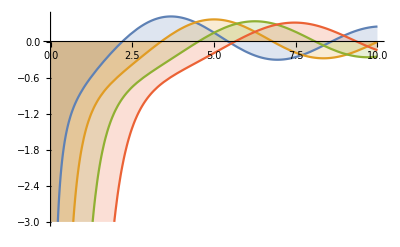

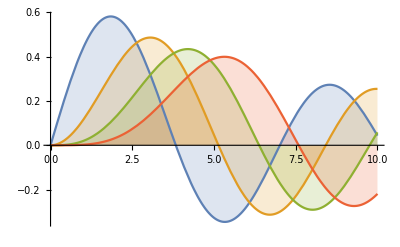

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

## Section five

```mathematica
Manipulate[Plot[Sin[a x+b],{x,0,6}],{{a,2,"Multiplier"},1,4},{{b,0,"Phase Parameter"},0,10}]
```

## Section six

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy.
		Lorem Ipsum

IdentityElement[group_]:=Module[{elems,n},Which[(*Groupes finis standard*)Head[group]===CyclicGroup,0,Head[group]===DihedralGroup,Cycles[{}],Head[group]===SymmetricGroup||Head[group]===AlternatingGroup,Cycles[{}],(*PermutationGroup*)Head[group]===PermutationGroup,Cycles[{}],(*AbelianGroup*)Head[group]===AbelianGroup||(ValueQ[AbelianGroupQ[_]]&&TrueQ[AbelianGroupQ[group]]),Table[0,{i,Length[group[[1]]]}],(*(Zn,+):groupe additif modulo n*)MatchQ[group,{"AddMod",n_}],0,(*(Zn,×) monoïde ou groupe multiplicatif*)MatchQ[group,{"MultMod",n_}],1,(*Cas général:prendre le premier élément de GroupElements*)True,First[GroupElements[group]]]]

IsIdentityByGroup[group_,elem_]:=(elem===IdentityElement[group])

IsIdentity[list_List,elem_,operation_:Plus]/;MemberQ[list,elem]:=AllTrue[list,((operation[elem,#])==#&)]

IsCenter[group_,elem_]/;GroupElementQ[group,elem]:=AllTrue[GroupElements[group],((PermutationProduct[elem,#])==PermutationProduct[#,elem]&)]

GroupCenter[group_]:=Select[GroupElements[group],IsCenter[group,#]&]

AbelianGroupQ[group_]:=GroupElements[group]==GroupCenter[group]

CayleyMultiplicationTable[group_]:=Module[{elements,Operation,n,i,table,opSymbol},(*Détection du type de groupe et définition de l'opération*)Which[(*Groupe abélien*)Head[group]===AbelianGroup||(ValueQ[AbelianGroupQ[_]]&&TrueQ[AbelianGroupQ[group]]),n=group[[1]];
elements=Tuples[Table[Range[0,n[[i]]-1],{i,Length[n]}]];
Operation[x_,y_]:=Mod[x+y,n];
opSymbol="+ (mod "<>ToString[n]<>")",(*Groupe cyclique*)Head[group]===CyclicGroup,elements=Range[0,group[[1]]-1];
Operation[x_,y_]:=Mod[x+y,group[[1]]];
opSymbol="+ (mod "<>ToString[group[[1]]]<>")",(*Groupes modulaires personnalisés*)MatchQ[group,{_String,_Integer}],elements=Range[0,group[[2]]-1];
Operation[x_,y_]:=Which[group[[1]]=="AddMod",Mod[x+y,group[[2]]],group[[1]]=="MultMod",Mod[x*y,group[[2]]]];
opSymbol=Which[group[[1]]=="AddMod","+ (mod "<>ToString[group[[2]]]<>")",group[[1]]=="MultMod","× (mod "<>ToString[group[[2]]]<>")"],(*Domaine Booléen*)MatchQ[group,{_String,_String}],elements={True,False};
Operation[x_,y_]:=Which[group[[1]]=="And",And[x,y],group[[1]]=="Or",Or[x,y],group[[1]]=="Xor",Xor[x,y]];
opSymbol=group[[1]],(*Groupes de permutations*)MemberQ[{DihedralGroup,SymmetricGroup,AlternatingGroup,PermutationGroup},Head[group]],elements=GroupElements[group];
Operation[x_,y_]:=PermutationProduct[x,y];
opSymbol="∘"];
(*Construction de la table avec en-têtes*)table=Prepend[MapIndexed[Prepend[#,elements[[First[#2]]]]&,Table[Operation[elements[[i]],elements[[j]]],{i,Length[elements]},{j,Length[elements]}]],Prepend[elements,Style[opSymbol,Bold]]  (*Case supérieure gauche avec couleur*)];
Grid[table,Frame->All,Spacings->{2,2}]]

background[val_,listeCouleurs_]:=Framed[val,Background->listeCouleurs[[val+1]]]

ColouredCayleyTable[{a_,n_Integer}]:=Module[{table,elements,couleurs},elements=Range[0,n-1];
couleurs=ColorData["AlpineColors"]/@Subdivide[0,1,n-1];
table=Prepend[MapIndexed[Prepend[#,elements[[First[#2]]]]&,Table[background[If[a ==="MultMod",Mod[Times[i,j],n], Mod[Plus[i,j],n]],couleurs],{i,0,n-1},{j,0,n-1}]],Prepend[elements,Style[If[a ==="MultMod","Multiplication Mod ", "Addition Mod "]<>ToString[n],Bold]]];
Grid[table,Frame->All,Spacings->{1,1}]]

fifteenPuzzle=Manipulate[
tileFaces=Flatten[ImagePartition[Graphics[{}],ImageDimensions[Graphics[{}]]/size]];
If[Length[puzzleGrid]=!=size,puzzleGrid=Partition[RandomSample[Range[size^2],size^2],size]];

Grid[Map[
tileButton[#,puzzleGrid,tileFaces,showLabels,size,
Enabled->Not[OrderedQ[Flatten[puzzleGrid]]],
Appearance->If[noEdges,Automatic,"Frameless"]]&,
puzzleGrid,{2}],Frame->All,Spacings->{1,1}],

{{size,4},Range[3,6],ControlType->PopupMenu},
{{noEdges,False,"show edges"},{True,False},ControlType->None},
{{showLabels,True,"show labels"},{True,False},ControlType->None},
Button["Randomise puzzle",puzzleGrid=Partition[RandomSample[Range[size^2],size^2],size]],

Initialization:>(
tileButton[n_,tile_,_,opts___]/;n==Max[tile]:=Button[" ",Null,Background->LightGray,Enabled->False];
tileButton[n_,tile_,tfc_,labelsShown_,size_,opts___]:=Button[If[labelsShown,Show[
Graphics[Inset[tfc[[n]],{0,0},{0,0},1]],
Graphics[{Text[Style[n,200/size/2],{0.5,0.5}]}],
PlotRange->{{0,1},{0,1}},ImageSize->100/size],
tfc[[n]]],tileMove[n,tile],FrameMargins->0,opts];
SetAttributes[tileButton,HoldRest];

borderingSquare[n_,tile_]:=Module[{posN,posMax,diff},posN=Flatten[Position[tile,n]];
posMax=Flatten[Position[tile,Max[tile]]];
diff=Abs[posN-posMax];
(Total[diff]==1)&&(Count[diff,1]==1)];
tileMove[n_,tile_]:=(If[borderingSquare[n,tile],Unevaluated[tile]=tile/. {n->Max[tile],Max[tile]->n}]);
SetAttributes[tileMove,HoldRest];)];
transfos={InfiniteLine[{{0,0},{1/2,(√3)/6}}],
InfiniteLine[{{1,0},{1/2,(√3)/6}}],
InfiniteLine[{{1/2,1},{1/2,0}}],
Arrow[Circle[{1/2,(√3)/6},0.2,{π/2,(7π)/6}]],
Arrow[Circle[{1/2,(√3)/6},0.15,{π/2,(11π)/6}]]};
triangle=
{{
Opacity[0.5],
Polygon[{
{0,0},
{1,0},
{1/2,(√3)/2}
}]},
{PointSize[Large],StandardRed,Point[{0,0}]},
{PointSize[Large],StandardGreen,Point[{1,0}]},
{PointSize[Large],StandardBlue,Point[{1/2,(√3)/2}]}
};